## The calutron

```mathematica
Clear["Global`*"]
```

## Text

A calutron was a type of mass spectrometer used during World War II to enrich uranium. Enriching uranium involves separating out the isotope 235 U from the rest of the sample (mainly composed of 238 U). In the calutron, a uranium atom was singly ionized (stripped of 1 electron), accelerated by an electric field E between two plates of potential difference V . The atom enters an area containing a uniform magnetic field B that is perpendicular to the velocity of the atom. The atom travels a circular path of radius R and ends its journey at a location determined by its mass, m, and the strength of the magnetic field, B.
An α-unit calutron operates with a magnetic field of 3200 gauss, and the collectors for the 235 U and 238 U isotopes are separated a distance (center to center), between 16.0 mm and 22.0 mm. The diameter of the isotopes’ trajectory cannot be larger than 2.6 m, and the maximum electric potential attainable is 40 kV. The masses of the 235 U and 238 U isotopes are  3.903 10^-25 kg and  3.953 10^-25 kg, respectively.

Goal: Estimate the required voltage V to obtain the isotopes’ separation within the range of parameters mentioned above. Indicate the separation between collectors used for your estimation.

-Graphics-

## Data

```mathematica
(* data={q->e, e->1.602 10^-19,u->1.660539 10^-27,m[U235]->235.043924 u, m[U238]->238.050785 u}  ; *)
data={q->e, e->1.602 10^-19,u->1.660539 10^-27,m[U235]->3.903 10^-25, m[U238]->3.953 10^-25}  ;
dataα={B->0.32};
dataβ={B->0.64};
```

## Solution

```mathematica
sola=Solve[1/2 mm v0^2== q V&&q v0 B== mm v0^2/r,{v0,r}][[2]];
```

```mathematica
R=r/.sola
```

(√2 √mm √V)/(B √q)

```mathematica
(√2 √mm √V)/(B √q)
```

(√2 √mm √V)/(B √q)

```mathematica
RU235=R/.{mm->m[U235]}//.data;
RU238=R/.{mm->m[U238]}//.data;
```

```mathematica
Δz=2(RU238-RU235)/.dataα/.{V->35000}
```

0.0164799

```mathematica
Δz=2(RU238-RU235)/.dataβ/.{V->35000}
```

0.00823994

```mathematica
RU235/.dataα/.{V->35000}
RU235/.dataβ/.{V->35000}
```

1.29053

0.645263

```mathematica
dd={2RU238,2(RU238-RU235)}/.dataα
```

{0.0138844 √V,0.0000880887 √V}

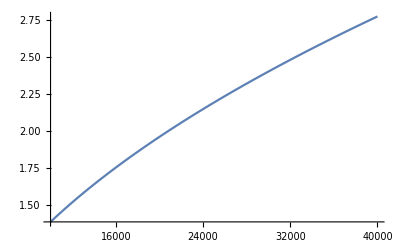

```mathematica
Plot[dd[[1]],{V,10000,40000}]
```

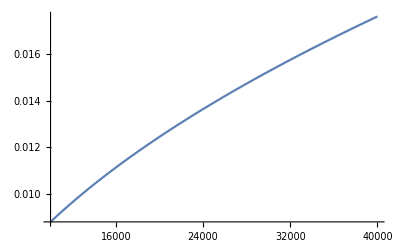

```mathematica
Plot[dd[[2]],{V,10000,40000}]
```

```mathematica
Solve[dd[[1]]==2.5,V]
```

{{V→32420.9}}

```mathematica
Solve[dd[[2]]==0.010,V]
```

{{V→12887.2}}

## Solution to the problem

```mathematica
Reduce[dd[[1]]≤2.6&&0.016≤dd[[2]]≤0.022,V]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

32991.3≤V≤35066.5

## Graphics

```mathematica
rU235[V_]=0.00689815643965238 √V;
rU238[V_]=0.006942200792360315 √V;
Δy[V_]=0.00008808870541586987 √V;
```

```mathematica
rr[r_,θ_]:={r Cos[θ],r (Sin[θ]-1)};
```

```mathematica
Manipulate[ParametricPlot[{rr[rU235[V],θ],rr[rU238[V],θ]},{θ,π/2,-π/2},PlotRange->{{0,2.7},{-2.8,0.1}},PlotStyle->{{Thin,Red},{Thin,Blue}},ImageSize->Large,PlotLabel->Style["Beams trajectories",Black,FontSize->12],
Epilog->Inset[GraphicsGrid[
{
{TextGrid[{
{Row[{Text["R_U235="],Text[NumberForm[rU235[V],{3,2}]],Text[" m" ]}]},
{Row[{Text["R_U238="],Text[Style[NumberForm[rU238[V],{3,2}],If[rU238[V]>1.3,Red,Black]]],Text[" m"]}]},
{Row[{Text["Δy="],Text[Style[NumberForm[Δy[V] 1000,{3,2}],If[Δy[V]<0.016,Red,Black]]],Text[" mm"]}]}}]},
{Plot[{0,Δy[V]1000},{x,0,.1},PlotStyle->{{Thick,Red},{Thick,Blue}},PlotRange->{-0.1,20},ImageSize->Medium,PlotLabel->Style["Collectors separation (mm)",Black,FontSize->12]]}
},Spacings->{1,-10},Frame->True],{1.7,-1.2},{0,0},1]
],{V,30000,40000}]
```

```mathematica
Framed[Row[{Text["Δy="],Δy[V]}]]
```

Δy=0.0000880887 √V

```mathematica
sola
```

{v0→(√2 √q √V)/(√mm),r→(√2 √mm √V)/(B √q)}